```mathematica
f[ν_]= Pi^(1/2) ϕ/(2^(ν-1)Gamma[ν+1/2]α^(2ν))
```

(2^(1-ν) √π α^(-2 ν) ϕ)/Gamma[1/2+ν]

```mathematica
FullSimplify[BesselK[-ν,x]]
```

BesselK[ν,x]

```mathematica
FullSimplify[BesselK[12/10,1]==BesselK[-12/10,1],x>0]
```

True

```mathematica
BesselK[-6/5,3/2]==BesselK[6/5,3/2]
```

BesselK[-6/5,3/2]==BesselK[6/5,3/2]

```mathematica
FullSimplify[Normal[Series[BesselK[ν,x],{x,0,1}]],ν∈Integers]
```

2^(-1-ν) x^ν Gamma[-ν]+2^(-1+ν) x^-ν Gamma[ν]

```mathematica
s
```

```mathematica
f1[x_,ν_]=2^-ν x^ν Gamma[-ν]
```

2^-ν x^ν Gamma[-ν]

```mathematica
Simplify[(x^ν f1[x,-ν]+x^ν f1[x,ν])/2,ν>0]
```

1/2 (2^-ν x^(2 ν) Gamma[-ν]+2^ν Gamma[ν])

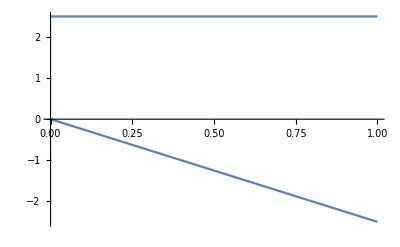

```mathematica
Plot[{x^ν  f1[x,ν],x^ν  f1[x,-ν]}/.ν->1/2,{x,0,1}]
```

```mathematica
f1[x_,ν_]=2^(-1-ν) x^ν Gamma[-ν]
```

```mathematica
hh[x_,ν_]=FullSimplify[Normal[Series[BesselK[ν,x],{x,0,1}]],ν>0&&x>0]
```

2^(-1-ν) x^ν Gamma[-ν]+2^(-1+ν) x^-ν Gamma[ν]

```mathematica
Manipulate[Plot[hh[x,ν],{x,0.001,1/2}],{ν,0.001,8}]
```

```mathematica
Manipulate[Plot[BesselK[ν,x],{x,0.001,1/2}],{ν,0.001,8}]
```

```mathematica
Manipulate[Plot[{hh[x,ν],BesselK[ν,x]},{x,0.001,1/2}],{ν,0.001,8}]
```

### Fonctions de Bessel et DL à l’ordre 1

```mathematica
DL1D1BesselK[ν_,x_]=FullSimplify[Normal[Series[D[BesselK[ν,x],x],{x,0,1}]],ν>0&&x>0]
```

2^(-3-ν) x^(-1-ν) (-x^(2 ν) (4 ν (1+ν)+x^2 (2+ν)) Gamma[-1-ν]+4^ν (x^2 (-2+ν)-4 (-1+ν) ν) Gamma[-1+ν])

### Fonctions de Matern et ses dérivées par rapport à x

```mathematica
ff[x_,v_]=x^v*BesselK[v,x];
dnff[x_,ν_,n_]:=FullSimplify[D[ff[x,ν],{x,n}],x>0&&ν>0];
d1ff[x_,ν_]=dnff[x,ν,1]
d2ff[x_,ν_]=dnff[x,ν,2]
```

-x^ν BesselK[-1+ν,x]

x^(-1+ν) (x BesselK[-2+ν,x]-BesselK[-1+ν,x])

```mathematica
d1ff[x,ν]
```

-x^ν BesselK[-1+ν,x]

```mathematica
d2ff[x,ν]
```

x^(-1+ν) (x BesselK[-2+ν,x]-BesselK[-1+ν,x])

```mathematica
ff[x,v]
```

ff[x,v]

```mathematica
Table[Limit[ff[x,ν],x->0],{ν,1/2,2,1/4}]
```

{√(π/2),Gamma[3/4]/2^(1/4),1,2^(1/4) Gamma[5/4],√(π/2),2^(3/4) Gamma[7/4],2}

```mathematica
Table[{ν,Limit[d1ff[x,ν],x->0]},{ν,1/2,2,1/4}]
```

{{1/2,-√(π/2)},{3/4,0},{1,0},{5/4,0},{3/2,0},{7/4,0},{2,0}}

```mathematica
Table[{ν,Limit[d2ff[x,ν],x->0]},{ν,1/2,2,1/4}]
```

{{1/2,√(π/2)},{3/4,-∞},{1,-∞},{5/4,-Gamma[1/4]/2^(3/4)},{3/2,-√(π/2)},{7/4,-Gamma[3/4]/2^(1/4)},{2,-1}}

```mathematica
Limit[d2ff[x,1.000001],x->0]
```

-500000.

```mathematica
d1ff[x,1]
```

-x BesselK[0,x]

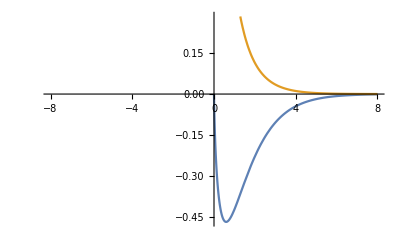

```mathematica
Plot[{-x BesselK[0,x],BesselK[0,x]},{x,-8,8}]
```

```mathematica
Normal[Series[BesselK[0,x],{x,0,1}]]
```

-EulerGamma+Log[2]-Log[x]

```mathematica
p[x_]:=FullSimplify[dnff[x,1.001,1]]
```

```mathematica
p[0]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::ivar: 0 is not a valid variable.

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

∂_{0,1} Indeterminate

```mathematica
p[x]
```

1.001 x^0.001 BesselK[1.001,x]-1/2 x^1.001 (BesselK[0.001,x]+BesselK[2.001,x])

```mathematica
Simplify[Normal[Series[d1ff[x,ν],{x,0,1}]],x>0&&ν>0]
```

(2^(-2-ν) (-x^(2 ν) (x^2+4 ν) Gamma[1-ν]-4^ν x^2 ν Gamma[-1+ν]))/(x ν)

```mathematica
K[t_,ν_]=f[ν]ff[α t,ν]
```

(2^(1-ν) √π α^(-2 ν) (t α)^ν ϕ BesselK[ν,t α])/Gamma[1/2+ν]

#### Cf page 32 Interpolation of Spatial Data

```mathematica
K[t,1/2]
```

(ⅇ^(-t α) π ϕ)/α

```mathematica
Simplify[K[t,3/2],t>0]
```

(ⅇ^(-t α) π (1+t α) ϕ)/(2 α^3)

```mathematica
FullSimplify[Series[K[t,ν],{t,0,2}],2<ν<3&&t>0&&α>0]
```

t^(2 ν) (2 ϕ Cos[π ν] Gamma[-2 ν]+(α^2 ϕ Cos[π ν] Gamma[-2 ν] t^2)/(2+2 ν)+O[t]^3)+((√π α^(-2 ν) ϕ Gamma[ν])/Gamma[1/2+ν]-((√π α^(2-2 ν) ϕ Gamma[-1+ν]) t^2)/(4 Gamma[1/2+ν])+O[t]^3)

```mathematica
exp1=FullSimplify[Normal[Series[K[t,ν],{t,0,2}]],2<ν<3&&t>0&&α>0]
```

1/4 α^(-2 ν) ϕ ((2 (t α)^(2 ν) (4+t^2 α^2+4 ν) Cos[π ν] Gamma[-2 ν])/(1+ν)-(√π (4+t^2 α^2-4 ν) Gamma[-1+ν])/Gamma[1/2+ν])

```mathematica
CoefficientList[exp1,t]
```

{(2 α^(-2 ν) (t α)^(2 ν) ϕ Cos[π ν] Gamma[-2 ν])/(1+ν)+(2 α^(-2 ν) (t α)^(2 ν) ν ϕ Cos[π ν] Gamma[-2 ν])/(1+ν)-(√π α^(-2 ν) ϕ Gamma[-1+ν])/Gamma[1/2+ν]+(√π α^(-2 ν) ν ϕ Gamma[-1+ν])/Gamma[1/2+ν],0,(α^(2-2 ν) (t α)^(2 ν) ϕ Cos[π ν] Gamma[-2 ν])/(2 (1+ν))-(√π α^(2-2 ν) ϕ Gamma[-1+ν])/(4 Gamma[1/2+ν])}

```mathematica
Simplify[CoefficientList[exp1,t].{1,t,t^2}==exp1]
```

True

```mathematica
FullSimplify[Normal[Series[K[t,ν],{t,0,2}]],2<ν<3&&t>0&&α>0]
```

```mathematica
ff[x,1/2]
```

ⅇ^-x √(π/2)

```mathematica
ff[x,3/2]
```

ⅇ^-x √(π/2) (1+1/x) x

### DL à l’ordre n autour de x=0 des fonctions de Matern et de ses dérivées par rapport à x

```mathematica
DL1ff0[x_,ν_]=FullSimplify[Normal[Series[ff[x,ν],{x,0,1}]],ν>0&&x>0]
```

2^(-1-ν) (x^(2 ν) Gamma[-ν]+4^ν Gamma[ν])

```mathematica
DLnDnBffn[x_,ν_,n_]:=Simplify[Normal[Series[dnff[x,ν,n],{x,0,n}]],ν>0&&x>0]
```

```mathematica
Manipulate[Plot[{DL1ff0[x,ν],ff[x,ν]},{x,0,1/2},PlotRange->All],{ν,0.001,8}]
```

#### DL à l’ordre 1 autour de x=0 de la dérivée par rapport à x à l’ordre 1

```mathematica
DL1D1Bff0[x_,ν_]=FullSimplify[DLnDnBffn[x,ν,1]]
```

-2^(-2+ν) x Gamma[-1+ν]+2^(-2-ν) x^(-1+2 ν) (x^2+4 ν) Gamma[-ν]

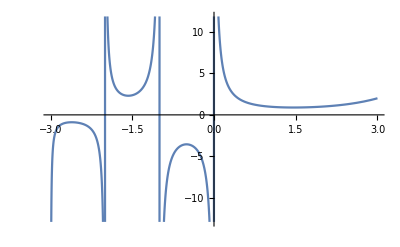

```mathematica
Plot[Gamma[x],{x,-3,3}]
```

```mathematica
d1ff[x,ν]
```

x^(-1+ν) ν BesselK[ν,x]+1/2 x^ν (-BesselK[-1+ν,x]-BesselK[1+ν,x])

```mathematica
Manipulate[Plot[{DL1D1Bff0[x,ν],d1ff[x,ν]},{x,0,1/2},PlotRange->All],{ν,0.001,8}]
```

#### DL à l’ordre 2 autour de x=0 de la dérivée par rapport à x à l’ordre 2

```mathematica
DL2D2ff0[x_,ν_]=FullSimplify[DLnDnBffn[x,ν,2]]
```

-2^(-2+ν) Gamma[-1+ν]+2^(-2-ν) x^(-2+2 ν) (x^2+4 ν (-1+2 ν)) Gamma[-ν]

```mathematica
Manipulate[Plot[{DL2D2ff0[x,ν],d2ff[x,ν]},{x,0,1/2},PlotRange->All],{ν,1.01,8}]
```

```mathematica
Table[Limit[DL1D2Bff0[x,ν],x->0],{ν,0,4,1/10}]
```

{ComplexInfinity,∞,∞,∞,∞,0,-∞,-∞,-∞,-∞,ComplexInfinity,0,0,0,0,0,0,0,0,0,ComplexInfinity,0,0,0,0,0,0,0,0,0,ComplexInfinity,0,0,0,0,0,0,0,0,0,ComplexInfinity}

```mathematica
Table[{ν,Limit[d1ff[x,ν],x->0],Limit[d2ff[x,ν],x->0]},{ν,0,2,1/10}]
```

{{0,-∞,∞},{1/10,-∞,∞},{1/5,-∞,∞},{3/10,-∞,∞},{2/5,-∞,∞},{1/2,-√(π/2),√(π/2)},{3/5,0,-∞},{7/10,0,-∞},{4/5,0,-∞},{9/10,0,-∞},{1,0,-∞},{11/10,0,-Gamma[1/10]/2^(9/10)},{6/5,0,-Gamma[1/5]/2^(4/5)},{13/10,0,-Gamma[3/10]/2^(7/10)},{7/5,0,-Gamma[2/5]/2^(3/5)},{3/2,0,-√(π/2)},{8/5,0,-Gamma[3/5]/2^(2/5)},{17/10,0,-Gamma[7/10]/2^(3/10)},{9/5,0,-Gamma[4/5]/2^(1/5)},{19/10,0,-Gamma[9/10]/2^(1/10)},{2,0,-1}}

#### DL à l’ordre 1 autour de x=0 des fonctions de Matern et de ses dérivées par rapport à x

```mathematica
Simplify[DL1DnBff0[x,1,1]]
```

x (EulerGamma+Log[x/2])

```mathematica
DL1DnBff0[x,2,2]
```

-1

```mathematica
Simplify[Normal[Series[dnff[x,1,1],{x,0,1}]],v>0&&x>0]
```

x (EulerGamma+Log[x/2])

```mathematica
Simplify[DL1DnBff0[x,ν,1]/.x->0,ν>1/2]
```

0

```mathematica
Simplify[DL1DnBff0[x,1/2,1]/.x->0]
```

-√(π/2)

```mathematica
Simplify[DL1DnBff0[x,ν,1]/.x->0,ν<1/2]
```

Simplify::infd: Expression 0^-1 + 2\ ν\ 2^-3 - ν\ (-4\ ν\ Gamma[1 - ν] + 4\ ν^2\ Gamma[-ν])/ν simplified to ComplexInfinity.

ComplexInfinity

```mathematica
Simplify[DL1DnBff0[1,x,1]]
```

(2^(-3-v) x^(-1+2 v) (-v x^2 Gamma[-1-v]-(4 v+x^2) Gamma[1-v]+4 v^2 Gamma[-v]))/v

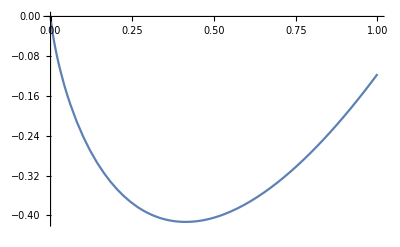

```mathematica
Plot[%,{x,0,1}]
```

```mathematica
Manipulate[Plot[ff[x,v],{x,0,8}],{v,0,8}]
```

### 2 m times differentiable if and only if v > m.

#### 2 times differentiable if and only if v > 1. (m=1)

```mathematica
Simplify[dnff[x,ν,1],x>0&&ν>0]
```

-1/2 x^(-1+ν) (x BesselK[-1+ν,x]-2 ν BesselK[ν,x]+x BesselK[1+ν,x])

```mathematica
Manipulate[Plot[{Evaluate[{dnff[x,ν,1],DL1DnBff0[x,ν,1]}]},{x,0,0.1}],{ν,1,8}]
```

```mathematica
Manipulate[Plot[{Evaluate[dnff[x,ν,1]],DL1D1BesselK[ν,x]},{x,0,8}],{ν,1,8}]
```

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
Simplify[dnff[x,ν,2],x>0&&ν>0]
```

1/4 x^(-2+ν) (x^2 BesselK[-2+ν,x]-4 x ν BesselK[-1+ν,x]+2 x^2 BesselK[ν,x]-4 ν BesselK[ν,x]+4 ν^2 BesselK[ν,x]-4 x ν BesselK[1+ν,x]+x^2 BesselK[2+ν,x])

```mathematica
Manipulate[Plot[Evaluate[dnff[x,ν,2]],{x,0,8},PlotRange->All],{ν,1,8}]
```

#### 4 times differentiable if and only if v > 2. (m=2)